# ログ分析：ユーザーキーワード連鎖、推測、レコメンド

## 変数

```mathematica
datestr="20231001"
```

20231001

```mathematica
dir="/Users/kouamano/NII/togo-log/rcoslogs/log/M=202310-202312/"
```

/Users/kouamano/NII/togo-log/rcoslogs/log/M=202310-202312/

```mathematica
datafile=dir<>"D="<>datestr<>"/T=4/_story/log-analysis_"<>datestr<>"_vocLGraph.save"
```

/Users/kouamano/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocLGraph.save

## Data

```mathematica
Get[datafile];
```

```mathematica
storyVocLGrSel[4,"voc"]["20231001"]//Length
```

121359

## Program

キーワードをグラフvertexのラベルにする：
CiNiiの場合、オプションがKWに後続するので "&" 以降は切って良い。

```mathematica
URLtoKW[v_String]:=Module[{l},
l=StringSplit[v,"?q="];
If[Length[l]<2,Null,StringSplit[l[[2]],"&"][[1]]//URLDecode]
]
URLtoKW[v_List]:=Module[{l},
l=StringSplit[v[[1]],"?q="];
If[Length[l]<2,Null,StringSplit[l[[2]],"&"][[1]]//URLDecode]
]
```

```mathematica
VtoVLRl[v_List]:=Map[#->URLtoKW[#]&,v]
```

```mathematica
GtoKWSeq[g_Graph]:=({URLtoKW[#1⟦1⟧],#1⟦2⟧}&)/@SortBy[Cases[VertexList[g],{_,{_}}],#1⟦2,1⟧&]
```

```mathematica
GtoKWSeq[g_Graph]:=({URLtoKW[#1⟦1⟧],#1⟦2⟧}&)/@SortBy[Cases[VertexList[g],{_,{__}}],#1⟦2,1⟧&]
```

## 試験

### ノード数

```mathematica
Map[VertexCount,storyVocLGrSel[4,"voc"]["20231001"]]//Tally
```

{{2,96834},{3,9483},{5,2225},{14,286},{10,587},{27,65},{16,221},{15,270},{4,3863},{8,893},{13,361},{7,1148},{20,136},{9,708},{17,187},{25,77},{6,1600},{51,10},{46,10},{11,472},{24,75},{36,26},{18,181},{23,92},{21,117},{57,9},{29,44},{12,382},{42,19},{41,10},{34,36},{19,150},{31,49},{44,8},{22,103},{70,4},{35,22},{52,10},{30,44},{33,31},{32,33},{28,56},{26,79},{53,9},{48,11},{38,21},{61,14},{43,17},{49,8},{135,1},{84,1},{67,8},{55,6},{94,2},{37,20},{39,27},{68,7},{121,2},{40,21},{50,5},{93,1},{132,1},{89,1},{119,1},{259,1},{59,3},{82,3},{56,6},{47,9},{64,1},{69,5},{95,2},{79,1},{108,1},{107,2},{78,3},{72,4},{66,5},{54,7},{87,2},{134,1},{105,1},{86,2},{74,4},{288,1},{297,1},{45,16},{60,5},{75,1},{63,6},{83,2},{101,1},{58,3},{151,1},{111,1},{396,1},{90,4},{140,1},{98,2},{130,1},{283,2},{273,1},{62,2},{117,1},{223,1},{96,1},{202,1},{200,1},{91,1},{118,1},{116,1},{114,1},{210,1},{92,1},{85,2},{65,5},{299,1},{1079,1},{80,2},{77,2},{113,1},{334,2},{230,1},{229,2},{262,1},{88,1},{73,1},{99,1},{157,1},{76,1},{170,1},{189,1},{160,1},{139,1},{115,1},{106,1},{285,1},{996,1}}

```mathematica
Position[Map[VertexCount,storyVocLGrSel[4,"voc"]["20231001"]],14][[1;;10]]
```

{{420},{704},{1297},{1304},{1364},{1404},{1413},{1527},{1700},{1962}}

### チェック

704 :

```mathematica
id=704
```

704

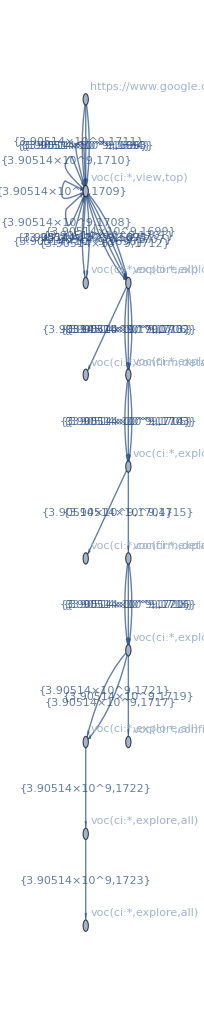

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->None]
```

VertexLabelとしてのvocを取り出す：

```mathematica
vocRl=PropertyValue[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels]
```

{Name,{https://cir.nii.ac.jp/all?q=hauptomann,{3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,view,top],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=6,{3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1522262180605190784,{3.90514×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1520291855057656576,{3.90514×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1020000781826138244,{3.90514×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=3,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=2,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=5,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=7,{3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=8,{3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=4,{3.90514×10^9}}→voc[ci:*,explore,all],https://www.google.com/→https://www.google.com/}

ラベルルール：

```mathematica
vl=VertexList[storyVocLGrSel[4,"voc"]["20231001"][[id]]]//VtoVLRl
```

{{https://cir.nii.ac.jp/,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→Null,https://www.google.com/→Null,{https://cir.nii.ac.jp/all?q=hauptomann,{3.90514×10^9,3.90514×10^9}}→hauptomann,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/crid/1020000781826138244,{3.90514×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=2,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=3,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/crid/1522262180605190784,{3.90514×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=4,{3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=5,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=6,{3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/crid/1520291855057656576,{3.90514×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=7,{3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=8,{3.90514×10^9}}→内野正幸}

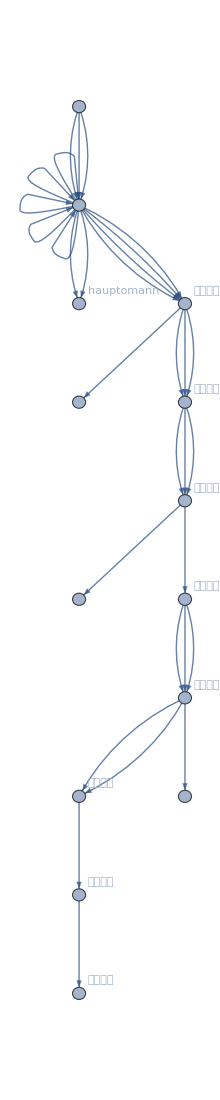

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->vl,EdgeLabels->None]
```

キーワードの時間的変遷：

```mathematica
GtoKWSeq[storyVocLGrSel[4,"voc"]["20231001"][[id]]]
```

{{hauptomann,{3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9}},{内野正幸,{3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9}},{内野正幸,{3.90514×10^9}},{内野正幸,{3.90514×10^9}}}

1297 :

```mathematica
id=1297
```

1297

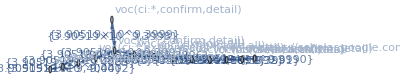

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->None]
```

VertexLabelとしてのvocを取り出す：

```mathematica
vocRl=PropertyValue[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels]
```

{Name,{https://cir.nii.ac.jp/all?q=bending+metals&count=20&sortorder=0,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=MATERIALS%20TRANSACTIONS,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1110845735210214784,{3.90519×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=bending+of+metal&count=20&sortorder=0,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/data,{3.90519×10^9}}→voc[ci:*,search,data],{https://cir.nii.ac.jp/crid/1390859160311309568,{3.90519×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=sheet+metal+bending&count=20&sortorder=0,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/articles?q=metal+bending,{3.90519×10^9}}→voc[ci:*,search,articles],{https://cir.nii.ac.jp/crid/1410291767736863363,{3.90519×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1390291767736863360,{3.90519×10^9,3.90519×10^9}}→voc[ci:*,confirm,detail],https://scholar.google.com/→https://scholar.google.com/,{https://cir.nii.ac.jp/dissertations?q=bending%20of%20metal&sortorder=0,{3.90519×10^9,3.90519×10^9}}→voc[ci:*,search,dssertations],{https://cir.nii.ac.jp/all?q=Journal%20of%20the%20Japan%20Institute%20of%20Metals%20and%20Materials,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1130000794770852224,{3.90519×10^9}}→voc[ci:*,confirm,detail]}

ラベルルール：

```mathematica
vl=VertexList[storyVocLGrSel[4,"voc"]["20231001"][[id]]]//VtoVLRl
```

{https://scholar.google.com/→Null,{https://cir.nii.ac.jp/crid/1130000794770852224,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/data,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/articles?q=metal+bending,{3.90519×10^9}}→metal bending,{https://cir.nii.ac.jp/crid/1390859160311309568,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/all?q=Journal%20of%20the%20Japan%20Institute%20of%20Metals%20and%20Materials,{3.90519×10^9}}→Journal of the Japan Institute of Metals and Materials,{https://cir.nii.ac.jp/all?q=bending+metals&count=20&sortorder=0,{3.90519×10^9}}→bending metals,{https://cir.nii.ac.jp/all?q=sheet+metal+bending&count=20&sortorder=0,{3.90519×10^9}}→sheet metal bending,{https://cir.nii.ac.jp/crid/1390291767736863360,{3.90519×10^9,3.90519×10^9}}→Null,{https://cir.nii.ac.jp/crid/1410291767736863363,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/all?q=MATERIALS%20TRANSACTIONS,{3.90519×10^9}}→MATERIALS TRANSACTIONS,{https://cir.nii.ac.jp/all?q=bending+of+metal&count=20&sortorder=0,{3.90519×10^9}}→bending of metal,{https://cir.nii.ac.jp/dissertations?q=bending%20of%20metal&sortorder=0,{3.90519×10^9,3.90519×10^9}}→bending of metal,{https://cir.nii.ac.jp/crid/1110845735210214784,{3.90519×10^9}}→Null}

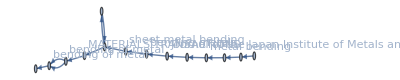

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->vl,EdgeLabels->None]
```

キーワードの時間的変遷：

```mathematica
GtoKWSeq[storyVocLGrSel[4,"voc"]["20231001"][[id]]]
```

{{Null,{3.90519×10^9}},{Null,{3.90519×10^9}},{metal bending,{3.90519×10^9}},{Null,{3.90519×10^9}},{Journal of the Japan Institute of Metals and Materials,{3.90519×10^9}},{bending metals,{3.90519×10^9}},{sheet metal bending,{3.90519×10^9}},{Null,{3.90519×10^9,3.90519×10^9}},{Null,{3.90519×10^9}},{MATERIALS TRANSACTIONS,{3.90519×10^9}},{bending of metal,{3.90519×10^9}},{bending of metal,{3.90519×10^9,3.90519×10^9}},{Null,{3.90519×10^9}}}

1304 :

```mathematica
id=1304
```

1304

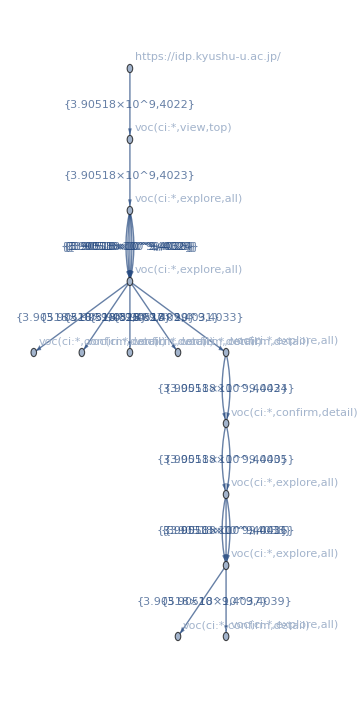

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->None]
```

VertexLabelとしてのvocを取り出す：

```mathematica
vocRl=PropertyValue[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels]
```

{Name,{https://cir.nii.ac.jp/,{3.90518×10^9}}→voc[ci:*,view,top],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1050001338899573376,{3.90518×10^9,3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1050858298305404032,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1390574334792671744,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1390565134833695232,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&hasLinkToFullText=true&count=20&sortorder=0,{3.90518×10^9,3.90518×10^9,3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A,{3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9}}→voc[ci:*,explore,all],https://idp.kyushu-u.ac.jp/→https://idp.kyushu-u.ac.jp/,{https://cir.nii.ac.jp/crid/1390853649717300224,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1050845763925213312,{3.90518×10^9}}→voc[ci:*,confirm,detail]}

ラベルルール：

```mathematica
vl=VertexList[storyVocLGrSel[4,"voc"]["20231001"][[id]]]//VtoVLRl
```

{https://idp.kyushu-u.ac.jp/→Null,{https://cir.nii.ac.jp/,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A,{3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/crid/1050858298305404032,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/crid/1390574334792671744,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/crid/1390853649717300224,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/crid/1390565134833695232,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/crid/1050001338899573376,{3.90518×10^9,3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&hasLinkToFullText=true&count=20&sortorder=0,{3.90518×10^9,3.90518×10^9,3.90518×10^9}}→自動車輸出,{https://cir.nii.ac.jp/crid/1050845763925213312,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→自動車輸出}

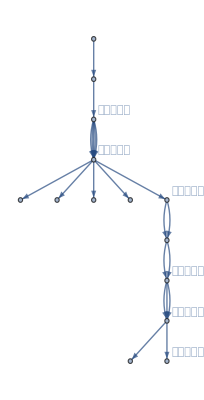

```mathematica
g=Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->vl,EdgeLabels->None]
```

キーワードの時間的変遷：

```mathematica
GtoKWSeq[storyVocLGrSel[4,"voc"]["20231001"][[id]]]
```

{{Null,{3.90518×10^9}},{中国自動車,{3.90518×10^9}},{中国自動車,{3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9}},{Null,{3.90518×10^9}},{Null,{3.90518×10^9}},{Null,{3.90518×10^9}},{Null,{3.90518×10^9}},{中国自動車,{3.90518×10^9}},{Null,{3.90518×10^9,3.90518×10^9}},{中国自動車,{3.90518×10^9,3.90518×10^9}},{自動車輸出,{3.90518×10^9,3.90518×10^9,3.90518×10^9}},{Null,{3.90518×10^9}},{自動車輸出,{3.90518×10^9}}}